```mathematica
Aatilda = 47 ;
Aptilda =0.05;
(* Aatilda = 48 ;
Aptilda =0.11; *)

deltaa=10^(-0.05 Aatilda)
```

0.00446684

```mathematica
deltap=(10^(0.05Aptilda)-1)/(10^(0.05 Aptilda)+1)
```

0.00287822

```mathematica
delta = Min[deltap,deltaa]
```

0.00287822

0.00287822

```mathematica
Aa= -20Log10[delta]
```

50.8175

```mathematica
Ap=20Log10[(1+delta)/(1- delta)]
```

0.05

```mathematica
alpha = 0.1102(Aa-8.7)
```

4.64135

```mathematica
Dv = (Aa-7.95)/14.36
```

2.9852

```mathematica
Nn=85;
```

```mathematica
Io[x_] := 1+ ∑_(k=1)^Infinity (1/(k!)(x/2)^k)^2
btt[n_]:=alpha √(1-((2n)/(Nn-1))^2)
Io[2.5]
```

3.28984

```mathematica
btt[1]
```

4.64006

```mathematica
Wk[n_]:=Io[btt[n]]/Io[alpha]
Table[Wk[x],{x,-42,42,2}]
```

{0.0504968,0.0791268,0.113271,0.152898,0.197823,0.247696,0.302009,0.3601,0.421162,0.484259,0.54835,0.612312,0.674968,0.735118,0.791573,0.843185,0.888883,0.9277,0.958805,0.981522,0.995355,1.,0.995355,0.981522,0.958805,0.9277,0.888883,0.843185,0.791573,0.735118,0.674968,0.612312,0.54835,0.484259,0.421162,0.3601,0.302009,0.247696,0.197823,0.152898,0.113271,0.0791268,0.0504968}

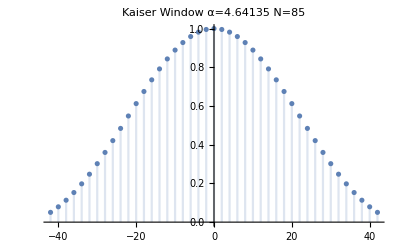

```mathematica
DiscretePlot[Wk[x],{x,-42,42,2},PlotLabel->"Kaiser Window \nα=4.64135\n N=85"]
```

100

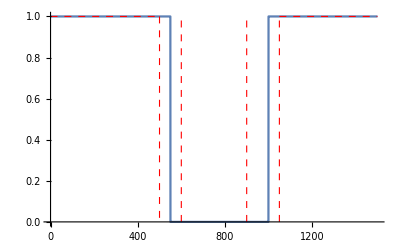

```mathematica
omegap1 = 500;
omegap2 = 1050;
omegaa1 = 600;
omegaa2 = 900;
omegas = 2800;

bt1 = omegaa1-omegap1;
bt2 = omegap2 - omegaa2;
btm=Min[bt1,bt2]
omegaC1= omegap1+btm/2;
omegaC2 = omegap2-btm/2;
H[w_]:=Piecewise[{{1,w<omegaC1},{1,w>omegaC2}}]

line1=Line[{{0,1},{500,1}}];
line2=Line[{{500,1},{500,0}}];
line3=Line[{{600,0},{600,1}}];
line4=Line[{{900,0},{900,1}}];
line6=Line[{{1050,0},{1050,1}}];
line5=Line[{{1050,1},{1500,1}}];
lineStyle={Thickness[0.002],Red,Dashed};
Plot[H[w],{w,0,1500},Exclusions->None,Epilog->{Directive[lineStyle],line1,line2,line3,line4,line5,line6}]
```

```mathematica
h[t_]:=InverseFourierTransform[H[ω],ω,t]
Abs[h[2]]
```

1/2 √(((-1+Cos[900])^2+Sin[900]^2)/(2 π))

```mathematica
DiscretePlot[Abs[h[n]],{n,0,200,2}]
```

$Aborted

```mathematica
T= 2Pi/omegas
```

π/1400

```mathematica
hantoni[n_]:=Piecewise[{{1+(2(omegaC1-omegaC2))/omegas,n==0},{1/(n Pi)(Sin[omegaC1 n T] - Sin[omegaC2 n T ]),True}}]
```

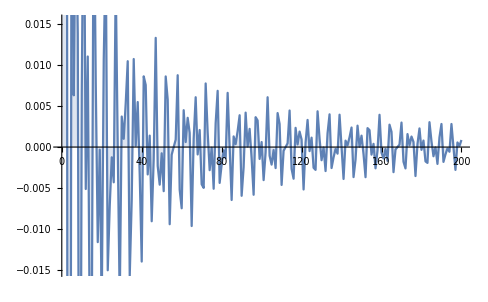

```mathematica
DiscretePlot[hantoni[n],{n,0,200}]
```

```mathematica
hkithmin[n_]:=Piecewise[{{1+(2(omegaC1-omegaC2))/omegas,n==0},{1/(n Pi)(Sin[omegaC1 n T] - Sin[omegaC2 n T ]+ Sin[omegas/2 n T]),True}}]
```

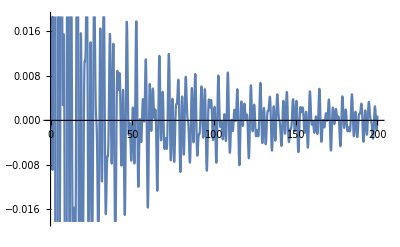

```mathematica
Plot[hkithmin[n],{n,0,200}]
```

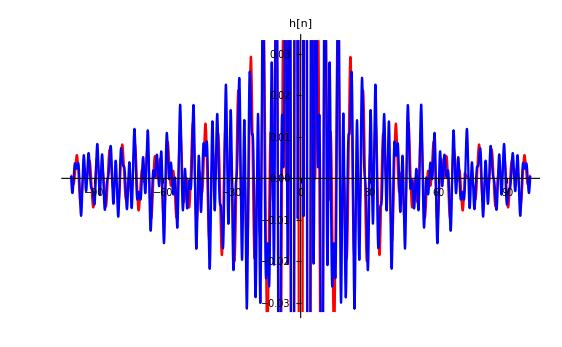

```mathematica
Plot[{hantoni[n],hkithmin[n]},{n,-100,100},PlotStyle->{Red,Blue},PlotLabel->"h[n]"]
```